```mathematica
(* Using the incidence data generated by the Gillespie stochastic simulation *)
```

```mathematica
(* These are for the largest aspirin dose, rowth to 10^2*)
```

```mathematica
(* No aspirin: Growth to 10^2 *) GTA[-1]=Import["INSERT PATH/r-path3-noasp.dat"];
(* 20-30 aspirin *) GTA[1]=Import["INSERT PATH/r-path3-asp-20.dat"];
(* 30-40 aspirin *) GTA[3]=Import["INSERT PATH/r-path3-asp-30.dat"];
(* 40-50 aspirin *) GTA[5]=Import["INSERT PATH/r-path3-asp-40.dat"];
(* 50-60 aspirin *) GTA[7]=Import["INSERT PATH/r-path3-asp-50.dat"];
(* 60-70 aspirin *) GTA[9]=Import["INSERT PATH/r-path3-asp-60.dat"];
(* 70-80 aspirin*) GTA[11]=Import["INSERT PATH/r-path3-asp-70.dat"];
```

```mathematica
Nexp=12;
```

```mathematica
GTA1=.;Do[ GTA1[ii]={}; Do[If[GTA[ii][[k]][[1]]>0,GTA1[ii]=Append[GTA1[ii],GTA[ii][[k]][[1]]]],{k,1,Length[GTA[ii]]}],{ii,-1,Nexp,2}];GTA2=.;Do[ GTA2[ii]=Sort[GTA1[ii]],{ii,-1,Nexp,2}];
```

```mathematica
Do[Do[x[j]=0,{j,1,80}]; Do[rr=Floor[GTA2[ii][[k]]]; Do[x[j]=x[j]+1,{j,rr+1,80}],{k,1,Length[GTA2[ii]]}]; Inc2[ii]=Table[x[j]/Length[GTA[ii]],{j,1,80}],{ii,-1,Nexp,2}]
```

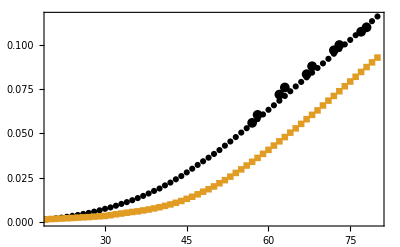
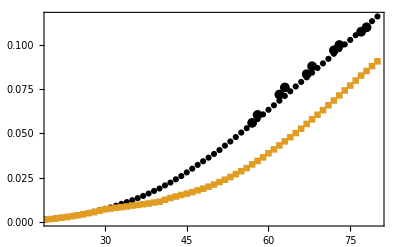
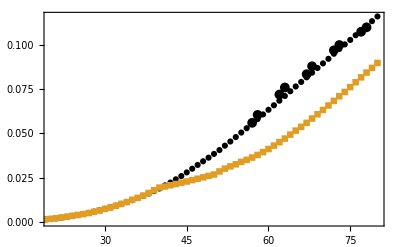
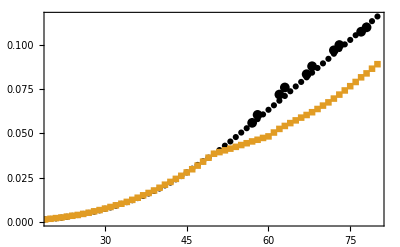
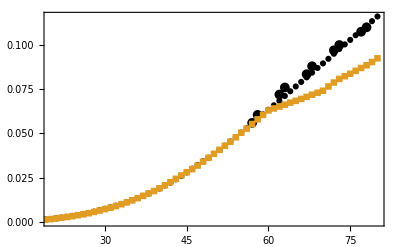
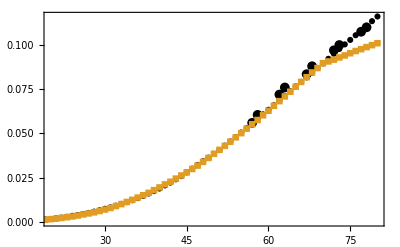

```mathematica
(* Figure 4(c) *) Table[Show[ListPlot[Inc2[-1],PlotRange->{{20,80},All},PlotStyle->Black,Frame->True,BaseStyle->Medium],ListPlot[{I*Inc2[-1],Inc2[2*j-1]},PlotRange->{{20,80},All},PlotMarkers->Automatic,Frame->True,BaseStyle->Medium],J0],{j,1,6}]
```

```mathematica
1.*Table[Inc2[2*j-1],{j,0,6}]
```

{{0.,0.,0.,0.,4.00002×10^-6,4.00002×10^-6,0.0000160001,0.0000240001,0.0000360001,0.0000600002,0.000104,0.000132001,0.000240001,0.000328001,0.000524002,0.000712003,0.000916004,0.001148,0.00140801,0.00168001,0.00200001,0.00240401,0.00288801,0.00342001,0.00388002,0.00449602,0.00506802,0.00579602,0.00654403,0.00740403,0.00818003,0.00914804,0.010176,0.01118,0.012264,0.0134601,0.0146961,0.0160561,0.0175121,0.0188721,0.0206321,0.0222321,0.0240801,0.0259121,0.0279841,0.0300801,0.0322081,0.0342721,0.0363041,0.0384242,0.0406122,0.0430922,0.0454562,0.0479602,0.0505122,0.0529562,0.0554962,0.0581162,0.0607722,0.0633883,0.0659163,0.0685163,0.0711883,0.0738483,0.0765723,0.0791323,0.0817203,0.0843763,0.0870043,0.0896124,0.0922044,0.0950644,0.0977804,0.100356,0.102884,0.105528,0.108248,0.110864,0.113492,0.116144},{0.,0.,0.,0.,0.,0.,0.000012,0.0000320001,0.0000560002,0.0000920004,0.000116,0.000208001,0.000308001,0.000416002,0.000548002,0.000716003,0.000892004,0.0011,0.00132401,0.00159601,0.00172401,0.00189601,0.00205601,0.00222001,0.00241601,0.00257601,0.00272401,0.00298801,0.00318401,0.00338801,0.00381602,0.00431202,0.00473602,0.00520002,0.00561202,0.00595602,0.00648003,0.00700003,0.00761203,0.00827603,0.00907204,0.00987604,0.0108,0.011824,0.0130361,0.0142161,0.0155921,0.0170761,0.0184761,0.0200561,0.0218401,0.0236121,0.0255961,0.0276921,0.0296801,0.0318561,0.0339721,0.0361921,0.0384762,0.0407362,0.0431642,0.0455482,0.0479522,0.0504602,0.0528882,0.0554122,0.0580722,0.0605162,0.0630483,0.0658243,0.0685643,0.0712163,0.0738763,0.0766963,0.0793723,0.0820443,0.0847803,0.0875284,0.0901924,0.0929004},{0.,0.,0.,0.,0.,0.,4.00002×10^-6,0.000012,0.0000320001,0.0000640003,0.000116,0.000176001,0.000276001,0.000376002,0.000504002,0.000636003,0.000808003,0.000996004,0.001224,0.00157201,0.00193601,0.00232401,0.00274401,0.00324001,0.00371601,0.00426802,0.00494402,0.00551202,0.00629203,0.00714003,0.00754803,0.00800403,0.00832803,0.00872403,0.00921204,0.00960004,0.010012,0.010396,0.01096,0.011384,0.0125041,0.0135081,0.0143401,0.0151921,0.0159921,0.0168321,0.0177961,0.0187561,0.0199201,0.0211121,0.0224761,0.0238521,0.0253601,0.0269761,0.0286521,0.0304201,0.0325041,0.0344881,0.0364961,0.0387762,0.0409882,0.0432162,0.0455362,0.0478682,0.0502322,0.0526922,0.0553842,0.0579802,0.0605842,0.0632043,0.0659283,0.0686363,0.0714723,0.0743243,0.0770563,0.0799083,0.0827163,0.0853403,0.0880724,0.0907564},{0.,0.,0.,0.,0.,0.,0.,0.,8.00003×10^-6,0.0000360001,0.0000600002,0.000132001,0.000232001,0.000380002,0.000512002,0.000668003,0.000864003,0.001124,0.00140801,0.00170001,0.00208001,0.00246401,0.00291201,0.00340801,0.00393602,0.00437202,0.00500402,0.00570802,0.00645203,0.00734003,0.00816003,0.00914404,0.010184,0.011232,0.0125241,0.0135921,0.0148561,0.0163081,0.0178681,0.0194041,0.0200041,0.0207041,0.0214041,0.0221601,0.0228441,0.0236161,0.0244001,0.0251881,0.0260401,0.0267801,0.0285161,0.0301121,0.0313961,0.0325561,0.0339321,0.0350921,0.0363881,0.0378642,0.0394642,0.0412162,0.0431322,0.0450722,0.0471002,0.0493482,0.0516162,0.0537522,0.0560042,0.0584442,0.0608642,0.0632843,0.0658203,0.0684163,0.0710163,0.0734843,0.0761883,0.0789723,0.0817003,0.0844163,0.0870723,0.0898764},{0.,0.,0.,0.,0.,4.00002×10^-6,8.00003×10^-6,0.0000160001,0.0000360001,0.0000600002,0.0001,0.000176001,0.000228001,0.000340001,0.000480002,0.000664003,0.000856003,0.001056,0.00138001,0.00176401,0.00214001,0.00250001,0.00299201,0.00346801,0.00392402,0.00451602,0.00517202,0.00596002,0.00668003,0.00752003,0.00842803,0.00937204,0.010268,0.011308,0.012472,0.0136641,0.0150281,0.0163561,0.0177521,0.0192921,0.0210361,0.0226081,0.0243281,0.0260561,0.0279601,0.0297681,0.0318241,0.0340601,0.0362961,0.0385282,0.0394562,0.0404602,0.0414162,0.0424322,0.0434482,0.0444762,0.0454962,0.0464322,0.0474642,0.0483442,0.0505242,0.0525722,0.0542482,0.0558562,0.0573962,0.0589522,0.0604402,0.0620082,0.0638283,0.0657443,0.0675763,0.0697123,0.0719603,0.0743083,0.0767283,0.0791083,0.0817363,0.0839603,0.0866083,0.0891604},{0.,0.,0.,0.,0.,8.00003×10^-6,8.00003×10^-6,0.0000160001,0.0000200001,0.0000480002,0.0000760003,0.000144001,0.000216001,0.000340001,0.000468002,0.000584002,0.000744003,0.000972004,0.00124,0.00155601,0.00193601,0.00236401,0.00278001,0.00322801,0.00378002,0.00428802,0.00491202,0.00561202,0.00639603,0.00721203,0.00802003,0.00894404,0.00998004,0.011056,0.01222,0.0134401,0.0147081,0.0161041,0.0174241,0.0190201,0.0206881,0.0224721,0.0243601,0.0262641,0.0280761,0.0298201,0.0318521,0.0340401,0.0362241,0.0384922,0.0407322,0.0430482,0.0452962,0.0478562,0.0504322,0.0527242,0.0553442,0.0579722,0.0604642,0.0630483,0.0641443,0.0652603,0.0662563,0.0674163,0.0684483,0.0695203,0.0707043,0.0719043,0.0730123,0.0741443,0.0766003,0.0787923,0.0808123,0.0823603,0.0837523,0.0854003,0.0870123,0.0885444,0.0903924,0.0924844},{0.,0.,0.,0.,0.,0.,4.00002×10^-6,8.00003×10^-6,0.0000160001,0.0000600002,0.0001,0.000148001,0.000212001,0.000308001,0.000416002,0.000556002,0.000752003,0.000996004,0.001244,0.00151201,0.00184801,0.00222401,0.00264801,0.00306801,0.00360401,0.00422802,0.00479602,0.00540802,0.00615202,0.00698403,0.00786003,0.00894404,0.010068,0.01128,0.012476,0.0137401,0.0150601,0.0164201,0.0179561,0.0194921,0.0211841,0.0226841,0.0244681,0.0262281,0.0280481,0.0299081,0.0318401,0.0339521,0.0361601,0.0385162,0.0407282,0.0429922,0.0453442,0.0478042,0.0501842,0.0527242,0.0552122,0.0576082,0.0602642,0.0628483,0.0656323,0.0682723,0.0709403,0.0735803,0.0764563,0.0791483,0.0817963,0.0844843,0.0869763,0.0897124,0.0907244,0.0917364,0.0929524,0.0941084,0.0953564,0.0966084,0.0976404,0.0988244,0.0999164,0.101012}}

```mathematica
(* In the following files odd numbers -> the smallest dose, even numbers --> the intermediate dose *)
```

```mathematica
(* 20-30 aspirin *) GTA[1]=Import["INSERT PATH/r-path8b-asp-20.dat"]; GTA[2]=Import["INSERT PATH/r-path9-asp-20.dat"];
(* 30-40 aspirin *) GTA[3]=Import["INSERT PATH/r-path8c-asp-30.dat"]; GTA[4]=Import["INSERT PATH/r-path9-asp-30.dat"];
(* 40-50 aspirin *) GTA[5]=Import["INSERT PATH/r-path8c-asp-40.dat"]; GTA[6]=Import["INSERT PATH/r-path9-asp-40.dat"];
(* 50-60 aspirin *) GTA[7]=Import["INSERT PATH/r-path8c-asp-50.dat"]; GTA[8]=Import["INSERT PATH/r-path9-asp-50.dat"];
(* 60-70 aspirin *) GTA[9]=Import["INSERT PATH/r-path8c-asp-60.dat"];GTA[10]=Import["INSERT PATH/r-path9-asp-60.dat"];
(* 70-80 aspirin *) GTA[11]=Import["INSERT PATH/r-path8c-asp-70.dat"]; GTA[12]=Import["INSERT PATH/r-path9-asp-70.dat"];
```

```mathematica
Nexp=12;
```

```mathematica
GTA1=.;Do[ GTA1[ii]={}; Do[If[GTA[ii][[k]][[1]]>0,GTA1[ii]=Append[GTA1[ii],GTA[ii][[k]][[1]]]],{k,1,Length[GTA[ii]]}],{ii,-1,Nexp}];GTA2=.;Do[ GTA2[ii]=Sort[GTA1[ii]],{ii,-1,Nexp}];
```

Part::partd: Part specification 0⟦1⟧ is longer than depth of object.

```mathematica
Do[Do[x[j]=0,{j,1,80}]; Do[rr=Floor[GTA2[ii][[k]]]; Do[x[j]=x[j]+1,{j,rr+1,80}],{k,1,Length[GTA2[ii]]}]; Inc7[ii]=Table[x[j]/Length[GTA[ii]],{j,1,80}],{ii,-1,Nexp}]
```

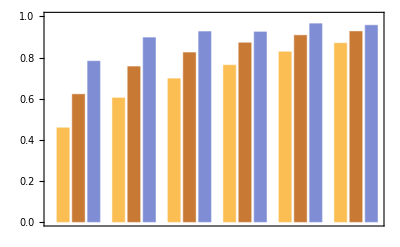

```mathematica
(* Figure 4(d) *) BarChart[1.*Table[{Inc2[2*jj-1][[20+10*jj]]/Inc2[-1][[20+10*jj]],Inc7[2*jj][[20+10*jj]]/Inc7[-1][[20+10*jj]],Inc7[2*jj-1][[20+10*jj]]/Inc7[-1][[20+10*jj]]},{jj,1,6}],Frame->True,BaseStyle->Medium,PlotRange->{0,1}]
```

```mathematica
1.*Table[{Inc2[2*jj-1][[20+10*jj]]/Inc2[-1][[20+10*jj]],Inc7[2*jj][[20+10*jj]]/Inc7[-1][[20+10*jj]],Inc7[2*jj-1][[20+10*jj]]/Inc7[-1][[20+10*jj]]},{jj,1,6}]
```

{{0.45759,0.620746,0.78228},{0.603222,0.755617,0.896565},{0.69696,0.823756,0.926086},{0.762668,0.871395,0.924495},{0.827389,0.907825,0.964623},{0.869713,0.926815,0.956828}}